# Cross-Sectional Analysis

### Initializing Cross-Sectional Data for the Sample

```mathematica
CrossSectionalData = ;
```

SPAC Name:			Name of the SPAC

deSPAC Name:			Name of the post-merger company

IPODate:			Date of the SPAC’s IPO

AcquisitionDeadlineDate: 	The acquisition deadline

MergerVoteDate: 		Date of the vote on the merger

IPOYear:			The year in which the SPAC went public

AcquisitionYear:		The year in which the SPAC carried out a merger

AnnouncementTiming:		the minimum of: the no. days between an IPO and the acquisition announcement date, or the no. of days between the acquisition announcement date and the merger deadline

DaysToAnnouncement:		No. of das from the IPO to the acquisition announcement

preVoteShareOverCash:	Share price of the SPAC one day before the merger vote minus the cash in trust per share

OneYearPerformance:		The performance of the post-merger company share price one year after the merger vote

OneYearAR:			The abnormal return (Russell 2000 as benchmark) of the post-merger company share price one year after the merger

IPOSize:			Public Proceeds from the SPAC’s IPO in million $

extraCashInTrust:		estimated redemption value per share minus 10$

SponsorOwnership:		Sponsor shares divided by public + sponsor shares

WarrantsOverPublicShares:	no. of warrants divided by the no. of public shares after the completion of the IPO

Rights:				dummy variable; 1 if rights are included in the units, 0 otherwise

SPACPeriodReturn:		The return earned on shares during the period from the IPO to the redemption deadline

SPACPeriodAR:			The AR earned on shares during the period from the IPO to the redemption deadline

IPOtoDeSPACReturn:		One-year post-merger return measured from the IPO of the SPAC

IPOtoDeSPACAR:		On-year post-merger AR measured from the IPO of the SPAC

TargetSize:			Combined Enterprise Value as implied by the merger transaction in million $

TargetROA:			Return on Assets of the target company for the last full year before the merger

TargetDebtRatio:		Debt Ratio based on the last annual financial statement before the merger

Target Industy:			Manufacturing, ConsumerAndServices, FinanceInsuranceRealEstate, Energy, HealthcarePharma, TechnologySpace, ShippingStorage

### Checking the pairwise scatterplot and correlation matrix for possible multi-colinearity and possible non-linear relationships

```mathematica
Needs["StatisticalPlots`"]
```

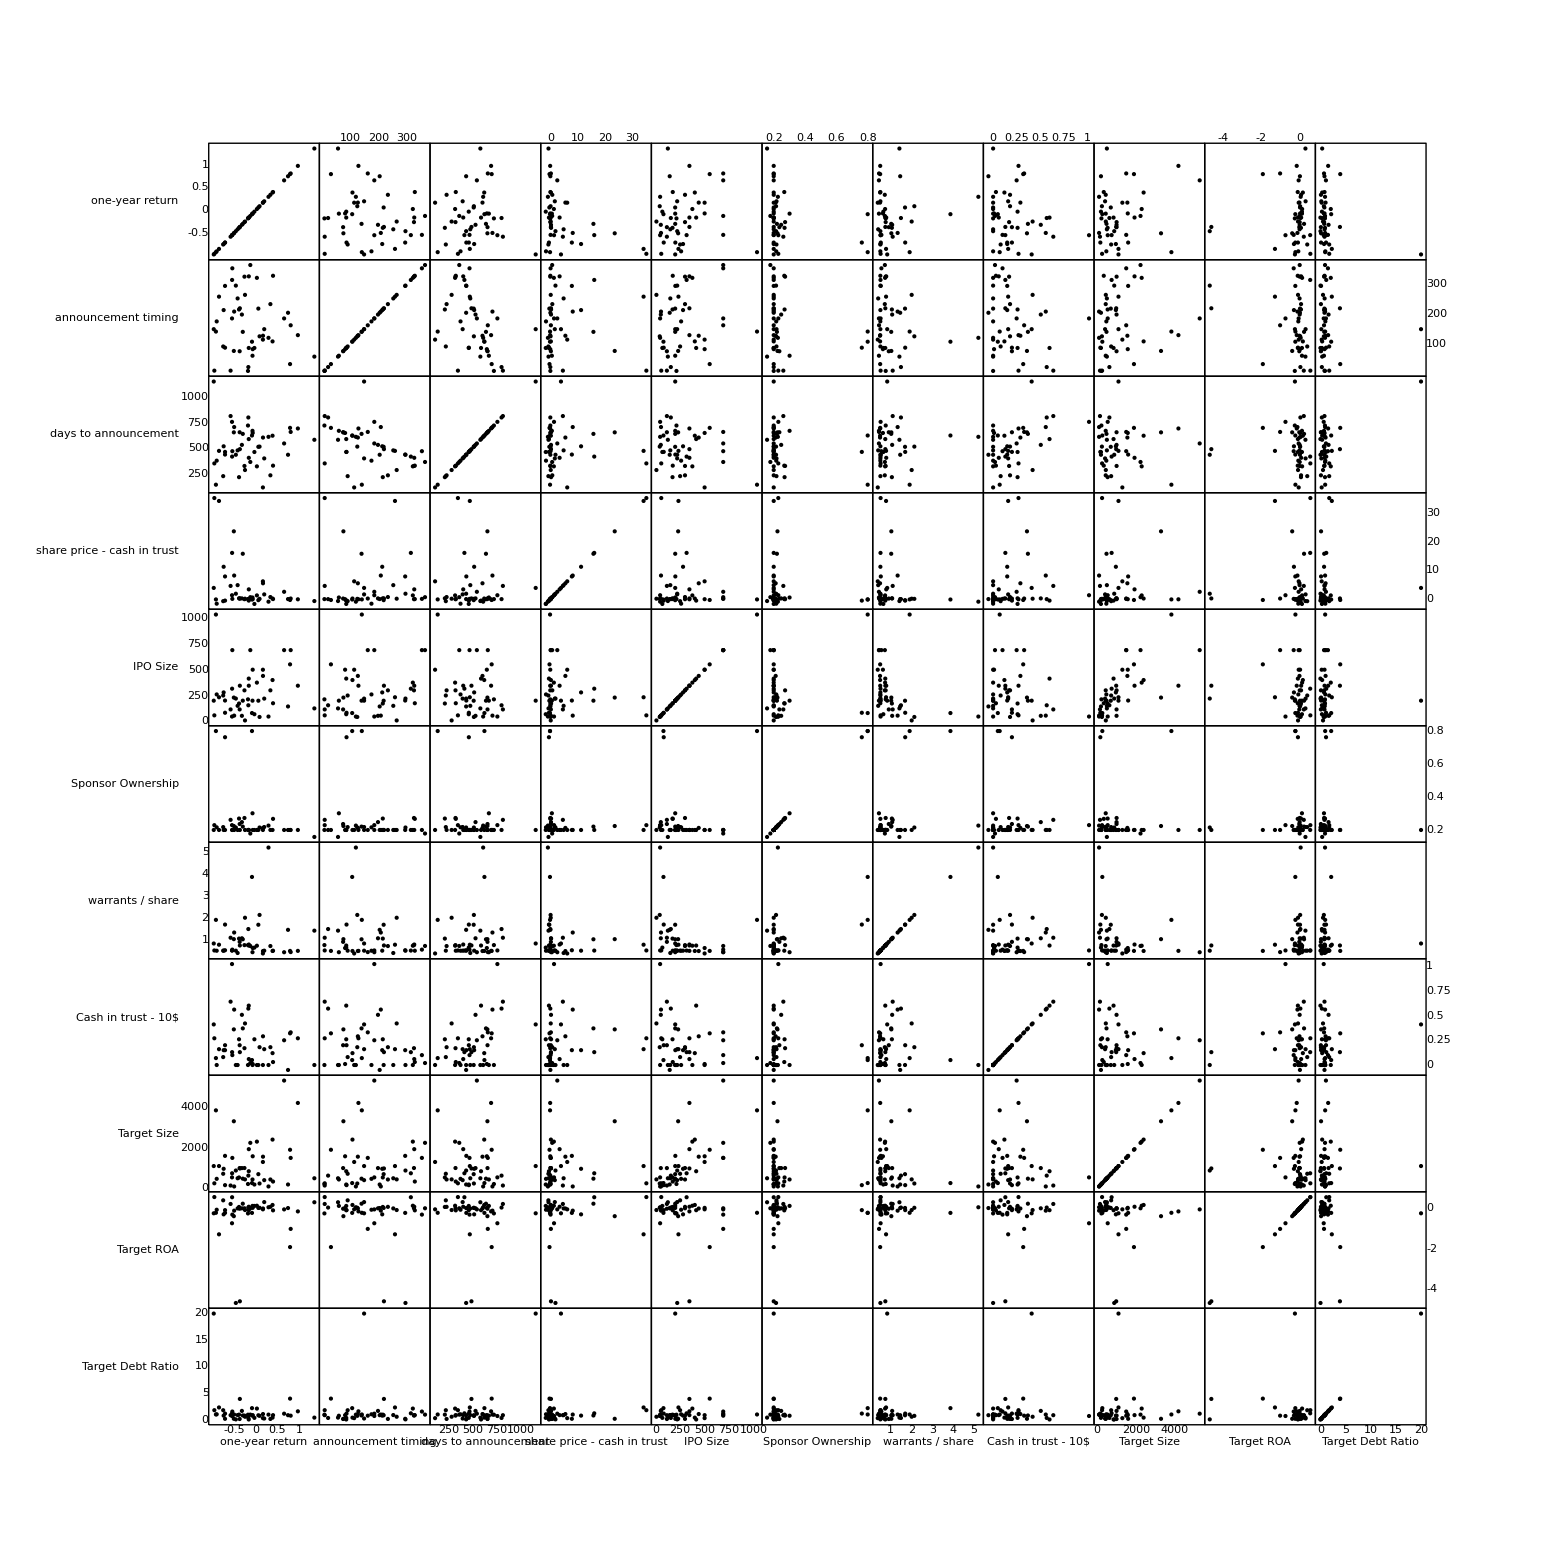

```mathematica
PairwiseScatterPlot[CrossSectionalData[#&, {#OneYearPerformance, #AnnouncementTiming, #DaysToAnnouncement, #preVoteShareOverCash, #IPOSize, #SponsorOwnership, #WarrantsOverPublicShares, #extraCashInTrust, #TargetSize, #TargetROA, #TargetDebtRatio}&]//Normal, DataTicks->True, DataLabels->{"one-year return", "announcement timing", "days to announcement", "share price - cash in trust", "IPO Size", "Sponsor Ownership", "warrants / share", "Cash in trust - 10$", "Target Size", "Target ROA", "Target Debt Ratio"}, ImageSize->1800]
```

There is a relationship between “AnnouncementTiming” and “DaysToAnnouncement” (also visible in the correlation matrix below) which was expected and is, why I planned to only include one of the two from the start. “DaysToAnnouncement” only exists in the dataset as a backup, in case “AnnouncementTiming” cannot be used as an explanatory variable for some reason.

No obvious patterns indicating a non-linear relationship are visible. The relationships between the dependent variable and the explanatory variables mostly seem to be quite weak.

### Correlation Matrix

```mathematica
TableForm[CrossSectionalData[Correlation[#,#]&, {#OneYearPerformance, #AnnouncementTiming,#DaysToAnnouncement, #preVoteShareOverCash, #IPOSize, #SponsorOwnership, #WarrantsOverPublicShares, #extraCashInTrust, #TargetSize, #TargetROA, #TargetDebtRatio}&]//Normal, TableHeadings->{{"one-year return", "announcement timing", "days to announcement", "share price - cash in trust", "IPO Size", "Sponsor Ownership", "warrants / share", "Cash in trust - 10$", "Target Size", "Target ROA", "Target Debt Ratio"},{"one-year return", "announcement timing", "days to announcement", "share price - cash in trust", "IPO Size", "Sponsor Ownership", "warrants / share", "Cash in trust - 10$", "Target Size", "Target ROA", "Target Debt Ratio"}}]
```

| one-year return | announcement timing | days to announcement | share price - cash in trust | IPO Size | Sponsor Ownership | warrants / share | Cash in trust - 10$ | Target Size | Target ROA | Target Debt Ratio
one-year return | 1. | -0.120364 | 0.0699614 | -0.396538 | 0.141405 | -0.237554 | 0.070473 | -0.179632 | 0.206498 | 0.0522878 | -0.217411
announcement timing | -0.120364 | 1. | -0.432961 | -0.014322 | 0.179358 | -0.158704 | -0.155704 | -0.235972 | 0.107514 | -0.166429 | -0.0235422
days to announcement | 0.0699614 | -0.432961 | 1. | -0.0147267 | -0.216919 | -0.144994 | 0.0775854 | 0.458432 | -0.0250059 | -0.0564801 | 0.468881
share price - cash in trust | -0.396538 | -0.014322 | -0.0147267 | 1. | -0.128146 | -0.126805 | -0.163915 | 0.107836 | 0.0219116 | 0.0372299 | 0.0322147
IPO Size | 0.141405 | 0.179358 | -0.216919 | -0.128146 | 1. | 0.105917 | -0.295817 | -0.221541 | 0.694511 | -0.115453 | -0.00530065
Sponsor Ownership | -0.237554 | -0.158704 | -0.144994 | -0.126805 | 0.105917 | 1. | 0.43847 | -0.0907858 | 0.0338702 | 0.043175 | -0.0122163
warrants / share | 0.070473 | -0.155704 | 0.0775854 | -0.163915 | -0.295817 | 0.43847 | 1. | -0.0877697 | -0.236825 | 0.110555 | -0.0176567
Cash in trust - 10$ | -0.179632 | -0.235972 | 0.458432 | 0.107836 | -0.221541 | -0.0907858 | -0.0877697 | 1. | -0.0489651 | 0.0316082 | 0.112413
Target Size | 0.206498 | 0.107514 | -0.0250059 | 0.0219116 | 0.694511 | 0.0338702 | -0.236825 | -0.0489651 | 1. | -0.0498115 | 0.0284607
Target ROA | 0.0522878 | -0.166429 | -0.0564801 | 0.0372299 | -0.115453 | 0.043175 | 0.110555 | 0.0316082 | -0.0498115 | 1. | -0.107704
Target Debt Ratio | -0.217411 | -0.0235422 | 0.468881 | 0.0322147 | -0.00530065 | -0.0122163 | -0.0176567 | 0.112413 | 0.0284607 | -0.107704 | 1.

### OLS Regression

```mathematica
lmCSR = LinearModelFit[CrossSectionalData[#&, { #AnnouncementTiming, #preVoteShareOverCash, #IPOSize, #SponsorOwnership, #WarrantsOverPublicShares, #Rights, #TargetSize, #TargetROA, #TargetDebtRatio, #Manufacturing, #ConsumerAndServices, #FinanceInsuranceRealEstate, #Energy, #HealthcarePharma, #TechnologySpace, #ShippingStorage, #OneYearPerformance}&]//Normal,{AnnouncementTiming, preVoteShareOverCash, IPOSize, SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetROA, TargetDebtRatio, Manufacturing, ConsumerAndServices, FinanceInsuranceRealEstate, Energy, HealthcarePharma, TechnologySpace, ShippingStorage},  {AnnouncementTiming, preVoteShareOverCash, IPOSize, SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetROA, TargetDebtRatio, Manufacturing, ConsumerAndServices, FinanceInsuranceRealEstate, Energy, HealthcarePharma, TechnologySpace, ShippingStorage}]
```

FittedModel[0.127669-0.000986105 AnnouncementTiming+0.189059 ConsumerAndServices+0.000528964 Energy+«16»+0.000105189 TargetSize+0.540181 TechnologySpace+0.111703 WarrantsOverPublicShares]

```mathematica
lmCSR//Normal
```

0.127669-0.000986105 AnnouncementTiming+0.189059 ConsumerAndServices+0.000528964 Energy+0.177664 FinanceInsuranceRealEstate-0.386441 HealthcarePharma+6.14327×10^-6 IPOSize+0.227693 Manufacturing-0.0278974 preVoteShareOverCash-0.0905228 Rights-0.0471956 ShippingStorage-1.48562 SponsorOwnership-0.0150699 TargetDebtRatio+0.0154881 TargetROA+0.000105189 TargetSize+0.540181 TechnologySpace+0.111703 WarrantsOverPublicShares

```mathematica
lmCSR["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.127669 | 0.670583 | 0.190385 | 0.85021
AnnouncementTiming | -0.000986105 | 0.000713161 | -1.38272 | 0.176324
preVoteShareOverCash | -0.0278974 | 0.00889654 | -3.13576 | 0.00366162
IPOSize | 6.14327×10^-6 | 0.00047799 | 0.0128523 | 0.989825
SponsorOwnership | -1.48562 | 0.587082 | -2.53051 | 0.0165065
WarrantsOverPublicShares | 0.111703 | 0.0993758 | 1.12405 | 0.269356
Rights | -0.0905228 | 0.216653 | -0.417824 | 0.678866
TargetSize | 0.000105189 | 0.0000837174 | 1.25648 | 0.218037
TargetROA | 0.0154881 | 0.0948379 | 0.163311 | 0.8713
TargetDebtRatio | -0.0150699 | 0.0286057 | -0.526817 | 0.601954
Manufacturing | 0.227693 | 0.606862 | 0.375197 | 0.70999
ConsumerAndServices | 0.189059 | 0.656283 | 0.288075 | 0.775147
FinanceInsuranceRealEstate | 0.177664 | 0.663307 | 0.267846 | 0.790537
Energy | 0.000528964 | 0.65639 | 0.000805867 | 0.999362
HealthcarePharma | -0.386441 | 0.740713 | -0.521716 | 0.605461
TechnologySpace | 0.540181 | 0.655921 | 0.823546 | 0.416294
ShippingStorage | -0.0471956 | 0.800407 | -0.0589645 | 0.953347

```mathematica
lmCSR["RSquared"]
```

0.55611

```mathematica
lmCSR["AdjustedRSquared"]
```

0.334165

### Scatterplot of the residuals to check for heteroskedasticity

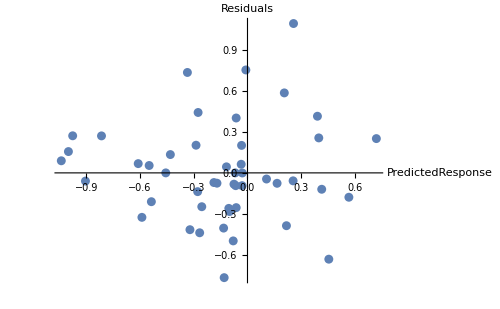

```mathematica
ListPlot[Transpose[{lmCSR["PredictedResponse"], lmCSR["FitResiduals"]}],AxesLabel->{"PredictedResponse", "Residuals"}, ImageSize->500]
```

The “fan-pattern” may indicate that heteroscedasticity is present. Thus,  a  Breusch-Pagan test is necessary.

```mathematica
lmBP = LinearModelFit[Transpose[{Normal[CrossSectionalData[All, "AnnouncementTiming"]], Normal[CrossSectionalData[All, "preVoteShareOverCash"]], Normal[CrossSectionalData[All, "IPOSize"]], Normal[CrossSectionalData[All, "SponsorOwnership"]], Normal[CrossSectionalData[All, "WarrantsOverPublicShares"]], Normal[CrossSectionalData[All, "Rights"]], Normal[CrossSectionalData[All, "TargetSize"]], Normal[CrossSectionalData[All, "TargetROA"]], Normal[CrossSectionalData[All, "TargetDebtRatio"]], Normal[CrossSectionalData[All, "Manufacturing"]], Normal[CrossSectionalData[All, "ConsumerAndServices"]], Normal[CrossSectionalData[All, "FinanceInsuranceRealEstate"]], Normal[CrossSectionalData[All, "Energy"]], Normal[CrossSectionalData[All, "HealthcarePharma"]], Normal[CrossSectionalData[All, "TechnologySpace"]], Normal[CrossSectionalData[All, "ShippingStorage"]],lmCSR["FitResiduals"]^2}], {AnnouncementTiming, preVoteShareOverCash, IPOSize, SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetROA, TargetDebtRatio, Manufacturing, ConsumerAndServices, FinanceInsuranceRealEstate, Energy, HealthcarePharma, TechnologySpace, ShippingStorage}, {AnnouncementTiming, preVoteShareOverCash, IPOSize, SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetROA, TargetDebtRatio, Manufacturing, ConsumerAndServices, FinanceInsuranceRealEstate, Energy, HealthcarePharma, TechnologySpace, ShippingStorage}]
```

FittedModel[0.0668094-0.000549926 AnnouncementTiming+0.375859 ConsumerAndServices+«18»+0.165165 TechnologySpace-0.00251309 WarrantsOverPublicShares]

```mathematica
testStatisticBP = With[{sqResids = lmCSR["FitResiduals"]^2}, (Variance[sqResids]*(Length[CrossSectionalData]-16)-Total[lmBP["FitResiduals"]^2])/2/(Total[sqResids]/Length[CrossSectionalData])^2]
```

-2.50064

```mathematica
pValBP = 1-CDF[ChiSquareDistribution[Length[lmCSR["BestFitParameters"]]-16], testStatisticBP]
```

1.

Since the P-Value of 1 is higher than any significance level used in statistics, the conclusion is, that heteroscedasticity is present.

### Attempting to fix the problem by using a log-lin model

Since I can’t apply a log transformation to the returns of the SPACs due to some of them being negative, I have to restate the dependent variable. To do that, I will index the the share price of the SPAC to 100 one day after the merger vote, and calculate the point score one year later based on the one-year post merger performance

#### Adding the new performance metric and its logarithm to the dataset

```mathematica
updatedCrossSectionalData = CrossSectionalData[All, Append[#, "PerformanceScore"->(#OneYearPerformance*100+100)]&];
```

```mathematica
updatedCrossSectionalData = updatedCrossSectionalData[All, Append[#, "logPerformanceScore"-> Log[#PerformanceScore]]&];
```

#### Scatterplot with the restated dependent variable to check for possible non-linear relationships

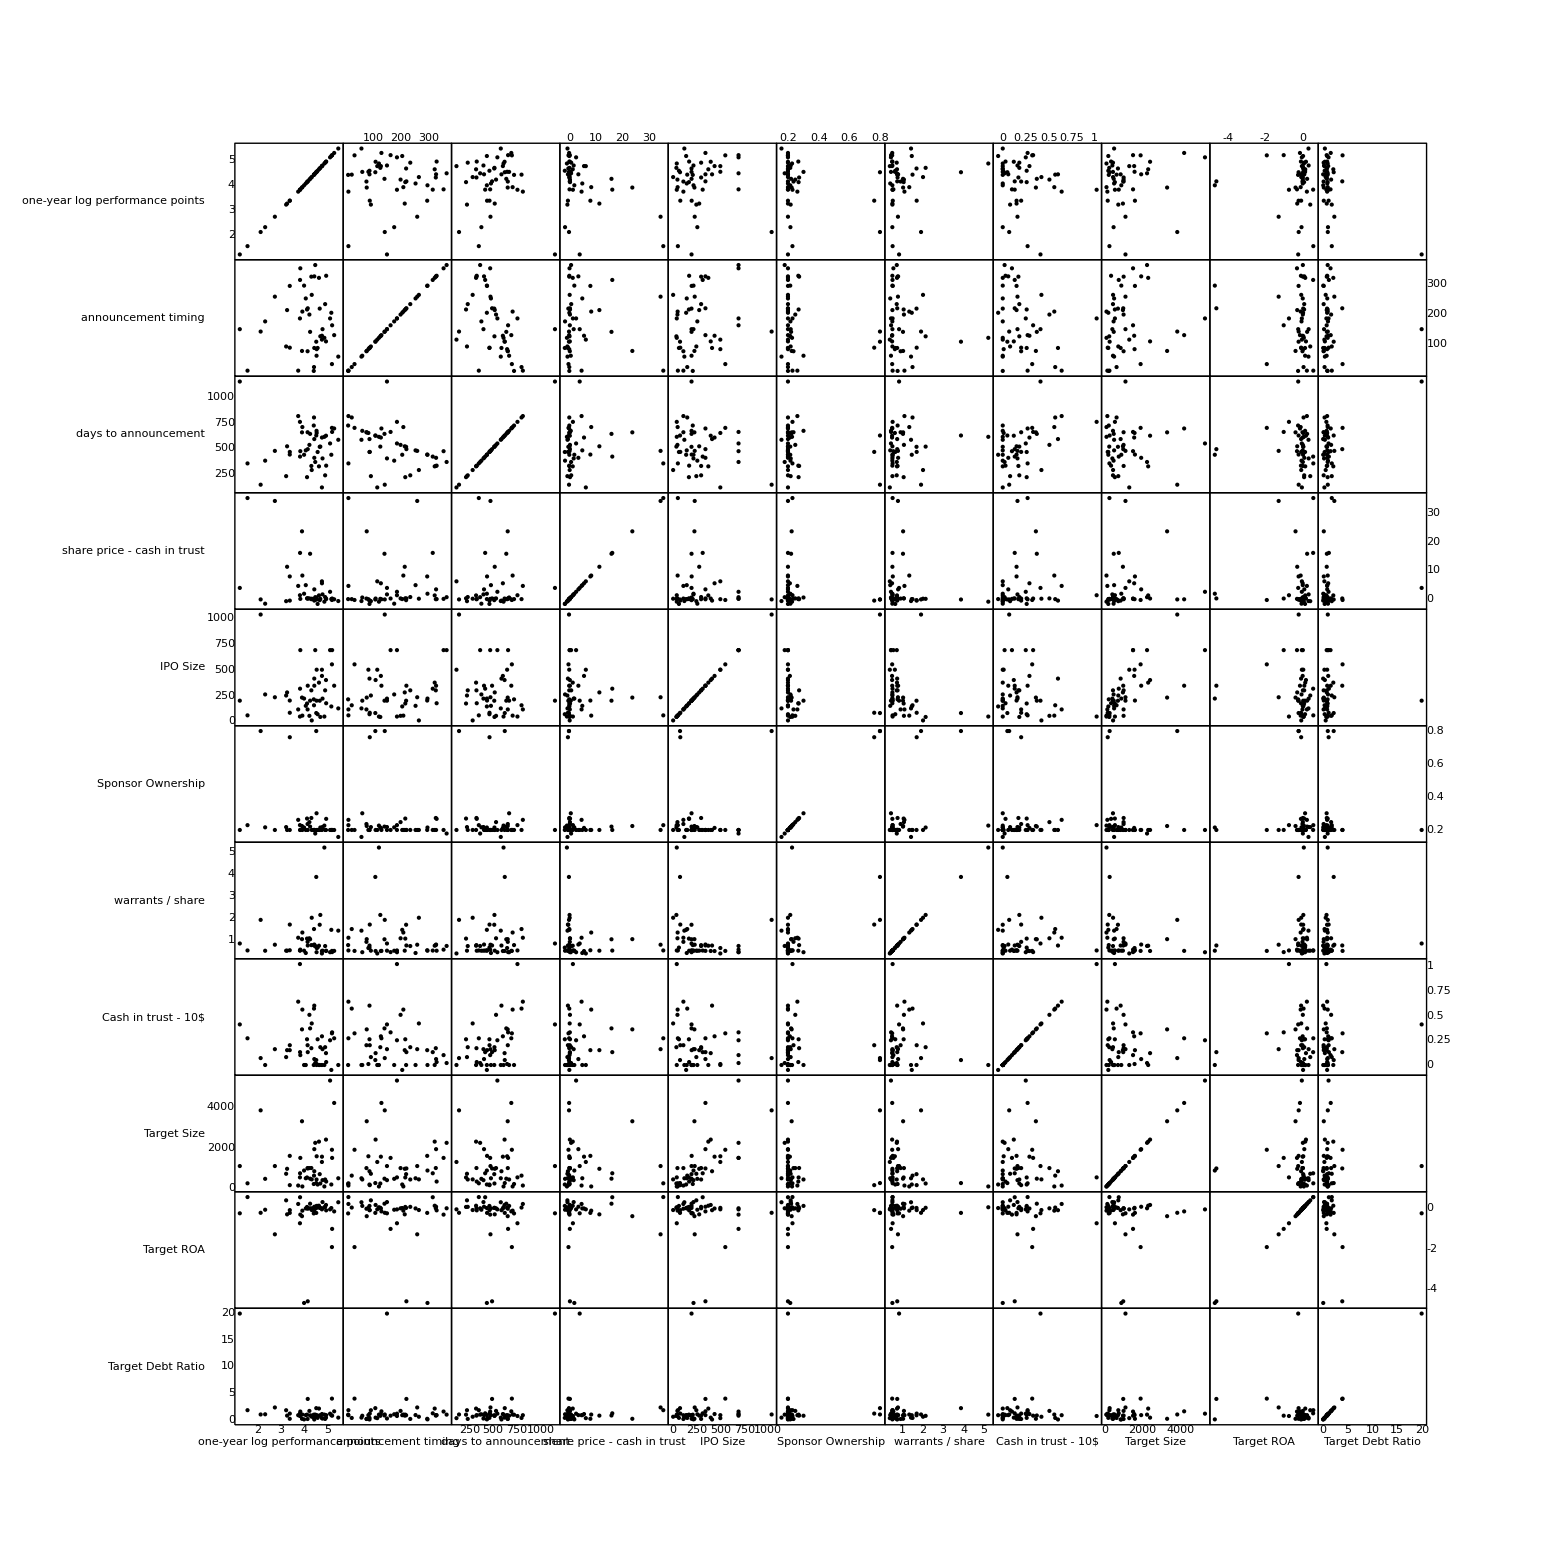

```mathematica
PairwiseScatterPlot[updatedCrossSectionalData[#&, {#logPerformanceScore, #AnnouncementTiming, #DaysToAnnouncement, #preVoteShareOverCash, #IPOSize, #SponsorOwnership, #WarrantsOverPublicShares, #extraCashInTrust, #TargetSize, #TargetROA, #TargetDebtRatio}&]//Normal, DataTicks->True, DataLabels->{"one-year log performance points", "announcement timing", "days to announcement", "share price - cash in trust", "IPO Size", "Sponsor Ownership", "warrants / share", "Cash in trust - 10$", "Target Size", "Target ROA", "Target Debt Ratio"}, ImageSize->1700]
```

There appears to be a non-linear relationship between “IPO Size” and the dependent variable. This can be fixed by taking the logarithm of “IPO Size”

The variance of the dependent variable appears to be decreasing with larger values for “announcement timing”. Since a positive correlation between variance of the dependent variable and an independent variable is fixed by taking the logarithm of the dependent variable, I theorize a negative correlation should be fixed by taking the log of the independent variable.

#### Adding the Log of “IPO Size” and “announcement timing” as variables and creating the updated scatterplot and correlation matrix

```mathematica
updatedCrossSectionalData = updatedCrossSectionalData[All, Append[#, "logIPOSize"-> Log[#IPOSize]]&];
updatedCrossSectionalData = updatedCrossSectionalData[All, Append[#, "logAnnouncementTiming"-> Log[#AnnouncementTiming]]&];
```

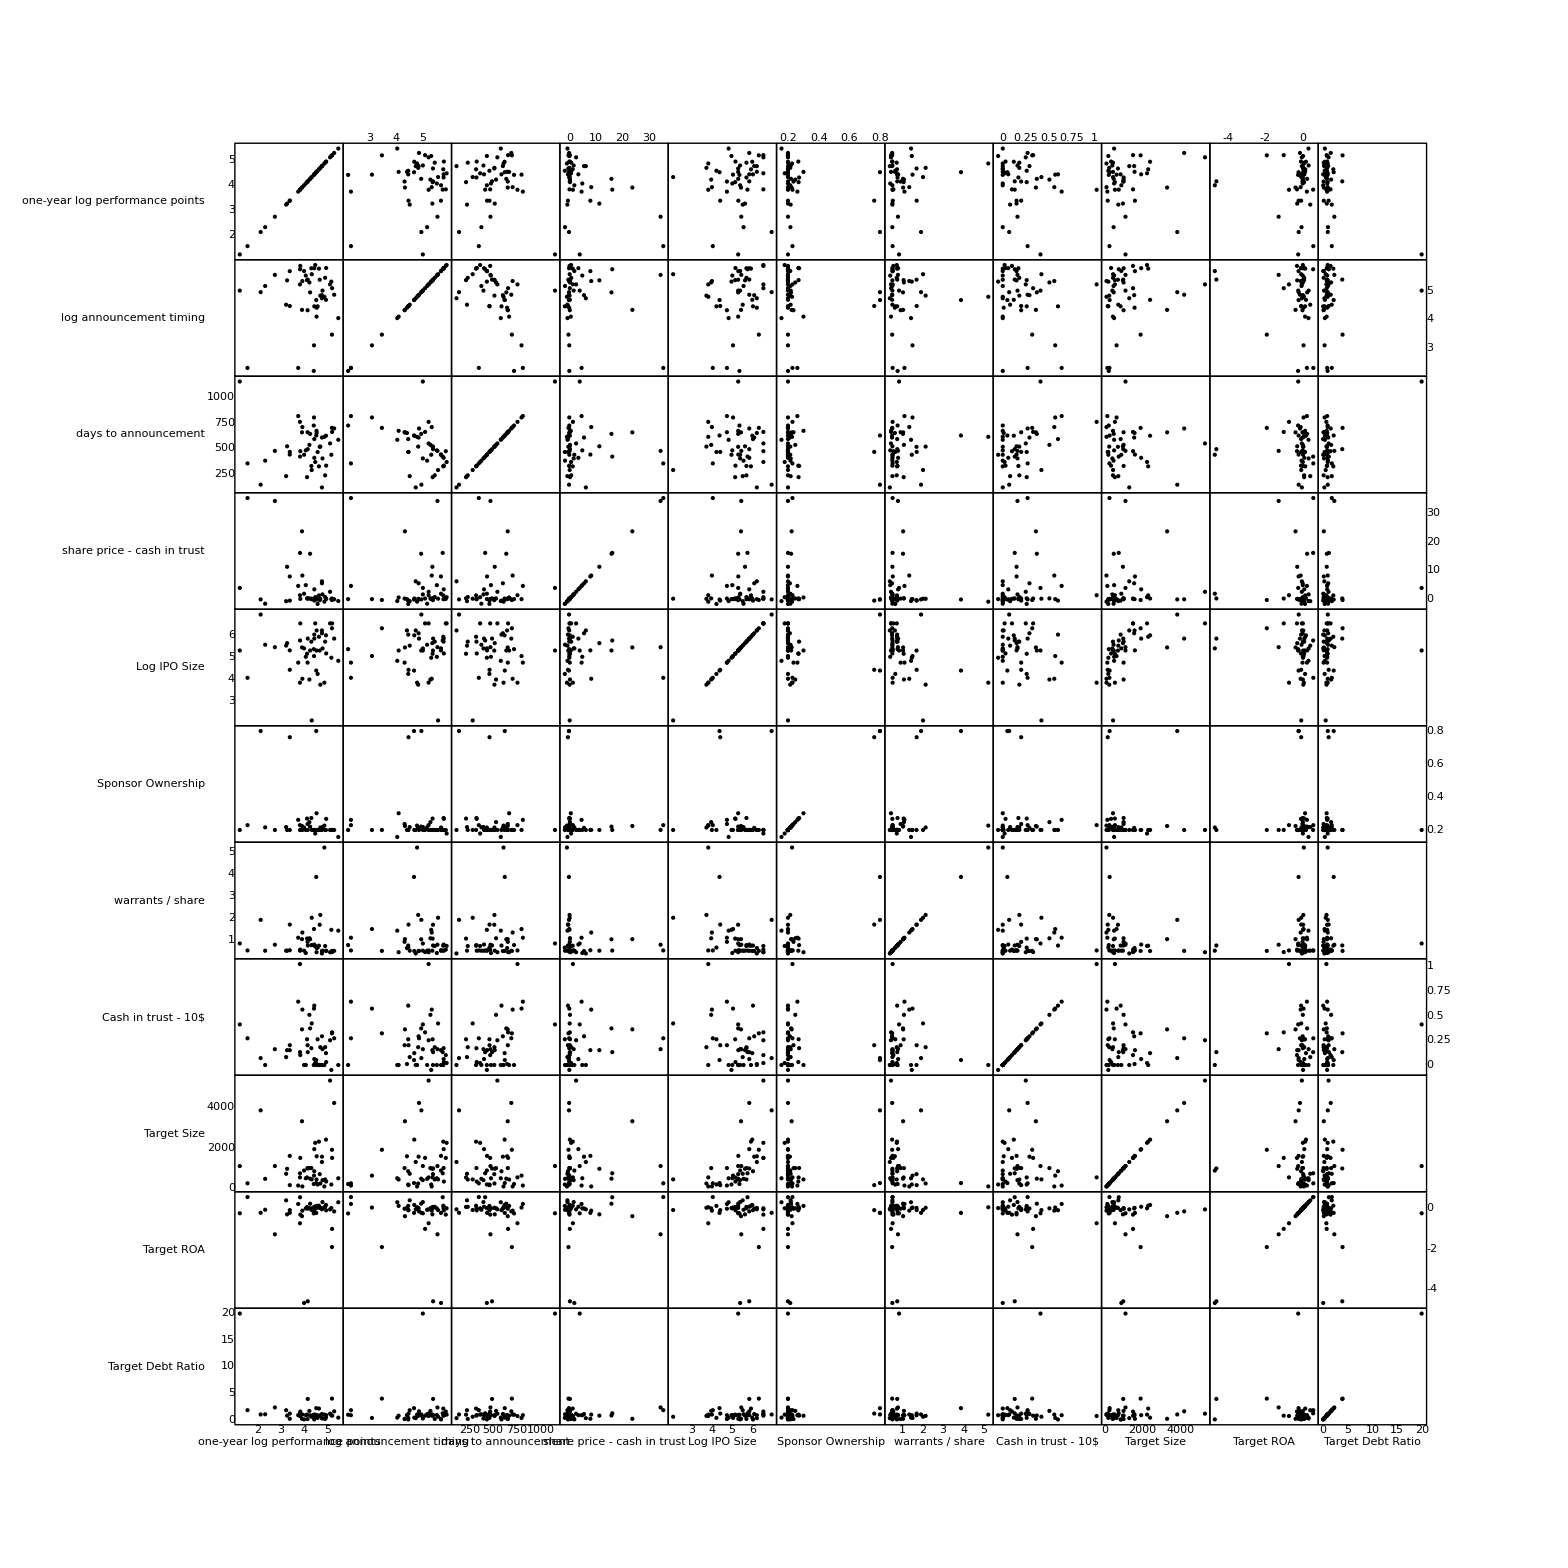

```mathematica
PairwiseScatterPlot[updatedCrossSectionalData[#&, {#logPerformanceScore, #logAnnouncementTiming, #DaysToAnnouncement, #preVoteShareOverCash, #logIPOSize, #SponsorOwnership, #WarrantsOverPublicShares, #extraCashInTrust, #TargetSize, #TargetROA, #TargetDebtRatio}&]//Normal, DataTicks->True, DataLabels->{"one-year log performance points", "log announcement timing", "days to announcement", "share price - cash in trust", "Log IPO Size", "Sponsor Ownership", "warrants / share", "Cash in trust - 10$", "Target Size", "Target ROA", "Target Debt Ratio"}, ImageSize->1700]
```

The obvious patterns indicating a non-linear relationship between “IPO Size” and the dependent variable as well as the one indicating a negative correlation between the variance of the dependent variable and “announcement timing” have disappeared. The log-transformation seems to have worked in both cases.

```mathematica
TableForm[updatedCrossSectionalData[Correlation[#,#]&, {#logPerformanceScore, #logAnnouncementTiming,#DaysToAnnouncement, #preVoteShareOverCash, #logIPOSize, #SponsorOwnership, #WarrantsOverPublicShares, #extraCashInTrust, #TargetSize, #TargetROA, #TargetDebtRatio}&]//Normal, TableHeadings->{{"log Performance", "log announcement timing", "days to announcement", "share price - cash in trust", "log IPO Size", "Sponsor Ownership", "warrants / share", "Cash in trust - 10$", "Target Size", "Target ROA", "Target Debt Ratio"},{"log Performance", "log announcement timing", "days to announcement", "share price - cash in trust", "log IPO Size", "Sponsor Ownership", "warrants / share", "Cash in trust - 10$", "Target Size", "Target ROA", "Target Debt Ratio"}}]
```

| log Performance | log announcement timing | days to announcement | share price - cash in trust | log IPO Size | Sponsor Ownership | warrants / share | Cash in trust - 10$ | Target Size | Target ROA | Target Debt Ratio
log Performance | 1. | 0.0822423 | -0.00646754 | -0.463728 | 0.0727596 | -0.241645 | 0.0896683 | -0.127265 | 0.0885769 | 0.00588623 | -0.470849
log announcement timing | 0.0822423 | 1. | -0.393432 | -0.126794 | 0.145031 | -0.0640052 | -0.0567136 | -0.216521 | 0.17155 | -0.155579 | 0.010725
days to announcement | -0.00646754 | -0.393432 | 1. | -0.0147267 | -0.11563 | -0.144994 | 0.0775854 | 0.458432 | -0.0250059 | -0.0564801 | 0.468881
share price - cash in trust | -0.463728 | -0.126794 | -0.0147267 | 1. | -0.0526215 | -0.126805 | -0.163915 | 0.107836 | 0.0219116 | 0.0372299 | 0.0322147
log IPO Size | 0.0727596 | 0.145031 | -0.11563 | -0.0526215 | 1. | -0.0416966 | -0.47032 | -0.33104 | 0.589136 | -0.146105 | 0.0412795
Sponsor Ownership | -0.241645 | -0.0640052 | -0.144994 | -0.126805 | -0.0416966 | 1. | 0.43847 | -0.0907858 | 0.0338702 | 0.043175 | -0.0122163
warrants / share | 0.0896683 | -0.0567136 | 0.0775854 | -0.163915 | -0.47032 | 0.43847 | 1. | -0.0877697 | -0.236825 | 0.110555 | -0.0176567
Cash in trust - 10$ | -0.127265 | -0.216521 | 0.458432 | 0.107836 | -0.33104 | -0.0907858 | -0.0877697 | 1. | -0.0489651 | 0.0316082 | 0.112413
Target Size | 0.0885769 | 0.17155 | -0.0250059 | 0.0219116 | 0.589136 | 0.0338702 | -0.236825 | -0.0489651 | 1. | -0.0498115 | 0.0284607
Target ROA | 0.00588623 | -0.155579 | -0.0564801 | 0.0372299 | -0.146105 | 0.043175 | 0.110555 | 0.0316082 | -0.0498115 | 1. | -0.107704
Target Debt Ratio | -0.470849 | 0.010725 | 0.468881 | 0.0322147 | 0.0412795 | -0.0122163 | -0.0176567 | 0.112413 | 0.0284607 | -0.107704 | 1.

#### Creating a new OLS regression

```mathematica
lmCSRlog = LinearModelFit[updatedCrossSectionalData[#&, { #logAnnouncementTiming, #preVoteShareOverCash, #logIPOSize, #SponsorOwnership, #WarrantsOverPublicShares, #Rights, #TargetSize, #TargetROA, #TargetDebtRatio, #Manufacturing, #ConsumerAndServices, #FinanceInsuranceRealEstate, #Energy, #HealthcarePharma, #TechnologySpace, #ShippingStorage, #logPerformanceScore}&]//Normal,{logAnnouncementTiming, preVoteShareOverCash, logIPOSize, SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetROA, TargetDebtRatio, Manufacturing, ConsumerAndServices, FinanceInsuranceRealEstate, Energy, HealthcarePharma, TechnologySpace, ShippingStorage},  {logAnnouncementTiming, preVoteShareOverCash, logIPOSize, SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetROA, TargetDebtRatio, Manufacturing, ConsumerAndServices, FinanceInsuranceRealEstate, Energy, HealthcarePharma, TechnologySpace, ShippingStorage}]
```

FittedModel[4.40262+0.522439 ConsumerAndServices+0.433253 Energy+«18»+0.0000560822 TargetSize+1.24965 TechnologySpace+0.18089 WarrantsOverPublicShares]

```mathematica
lmCSRlog//Normal
```

4.40262+0.522439 ConsumerAndServices+0.433253 Energy+0.740781 FinanceInsuranceRealEstate-0.0549416 HealthcarePharma+0.024414 logAnnouncementTiming-0.0611324 logIPOSize+0.779575 Manufacturing-0.0488078 preVoteShareOverCash-0.394769 Rights+0.733697 ShippingStorage-2.17118 SponsorOwnership-0.120576 TargetDebtRatio-0.0435161 TargetROA+0.0000560822 TargetSize+1.24965 TechnologySpace+0.18089 WarrantsOverPublicShares

```mathematica
lmCSRlog["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.40262 | 1.29294 | 3.40512 | 0.00179801
logAnnouncementTiming | 0.024414 | 0.107346 | 0.227432 | 0.821534
preVoteShareOverCash | -0.0488078 | 0.0127962 | -3.81425 | 0.00058843
logIPOSize | -0.0611324 | 0.154175 | -0.396514 | 0.694358
SponsorOwnership | -2.17118 | 0.845448 | -2.56808 | 0.0150987
WarrantsOverPublicShares | 0.18089 | 0.154354 | 1.17192 | 0.249883
Rights | -0.394769 | 0.310881 | -1.26984 | 0.213299
TargetSize | 0.0000560822 | 0.000105807 | 0.530043 | 0.599741
TargetROA | -0.0435161 | 0.133653 | -0.325591 | 0.746853
TargetDebtRatio | -0.120576 | 0.0409635 | -2.94349 | 0.00599745
Manufacturing | 0.779575 | 0.852227 | 0.914751 | 0.367164
ConsumerAndServices | 0.522439 | 0.921004 | 0.56725 | 0.574502
FinanceInsuranceRealEstate | 0.740781 | 0.934347 | 0.792833 | 0.433715
Energy | 0.433253 | 0.91117 | 0.475491 | 0.637667
HealthcarePharma | -0.0549416 | 1.04382 | -0.052635 | 0.95835
TechnologySpace | 1.24965 | 0.918042 | 1.36121 | 0.182955
ShippingStorage | 0.733697 | 1.10533 | 0.663783 | 0.511584

```mathematica
lmCSRlog["RSquared"]
```

0.691402

```mathematica
lmCSRlog["AdjustedRSquared"]
```

0.537103

#### Checking the Residual Plot for a pattern that could indicate heteroskedasticity

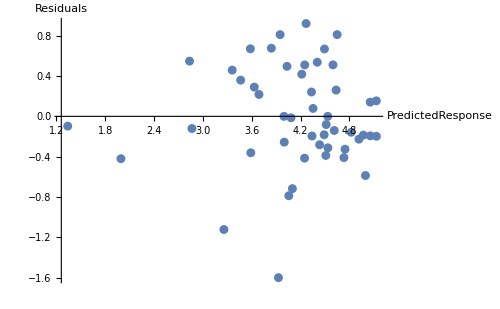

```mathematica
ListPlot[Transpose[{lmCSRlog["PredictedResponse"], lmCSRlog["FitResiduals"]}],AxesLabel->{"PredictedResponse", "Residuals"}, ImageSize->500]
```

The “Fan-Pattern” is gone, the transformation has worked.

#### Checking the Quantile Plot for an indication of non-normality and performing a Jarque-Bera Test

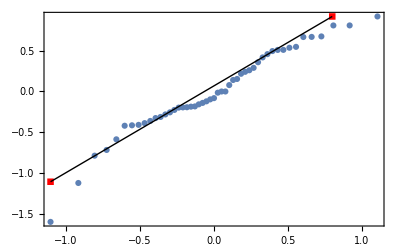

```mathematica
QuantilePlot[{lmCSRlog["FitResiduals"]}, PlotMarkers->Automatic, ReferenceLineStyle->Directive[Dashing[0], Red, Thick]]
```

```mathematica
pValJB = JarqueBeraALMTest[lmCSRlog["FitResiduals"]]
```

0.090281

The P-Value for the Jarque-Bera test indicates Skewness and excess Kurtosis  not to be equal to zero at a 10% level of significance.

According to my notes from last years statistics class this is only an issue when calculating prediction bands. Since no prediction bands are calculated in this analysis, the Skewness and/or excess Kurtosis is not addressed.

#### Removing Target Industries from the model, since those appear to not be significant

```mathematica
lmCSRlogNoIndustry = LinearModelFit[updatedCrossSectionalData[#&, { #logAnnouncementTiming, #preVoteShareOverCash, #logIPOSize, #SponsorOwnership, #WarrantsOverPublicShares, #Rights, #TargetSize, #TargetROA, #TargetDebtRatio, #logPerformanceScore}&]//Normal,{logAnnouncementTiming, preVoteShareOverCash, logIPOSize, SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetROA, TargetDebtRatio},  {logAnnouncementTiming, preVoteShareOverCash, logIPOSize, SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetROA, TargetDebtRatio}]
```

FittedModel[4.7662-0.0314574 logAnnouncementTiming+«11»+0.0000916712 TargetSize+0.302263 WarrantsOverPublicShares]

```mathematica
lmCSRlogNoIndustry["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.7662 | 0.937858 | 5.08201 | 9.66536×10^-6
logAnnouncementTiming | -0.0314574 | 0.106642 | -0.294982 | 0.769572
preVoteShareOverCash | -0.0493123 | 0.0119207 | -4.13669 | 0.000181584
logIPOSize | 0.0365522 | 0.147593 | 0.247655 | 0.8057
SponsorOwnership | -2.39717 | 0.793591 | -3.02066 | 0.0044356
WarrantsOverPublicShares | 0.302263 | 0.139483 | 2.16702 | 0.0364025
Rights | -0.45107 | 0.312088 | -1.44533 | 0.156353
TargetSize | 0.0000916712 | 0.000105435 | 0.869458 | 0.389917
TargetROA | -0.0188161 | 0.0960281 | -0.195944 | 0.845671
TargetDebtRatio | -0.152179 | 0.0330951 | -4.59823 | 0.0000440954

```mathematica
lmCSRlogNoIndustry["RSquared"]
```

0.598123

```mathematica
lmCSRlogNoIndustry["AdjustedRSquared"]
```

0.505382

#### Removing log IPO Size, since it is not significant

```mathematica
lmCSRlogNoIndustryNoIPO = LinearModelFit[updatedCrossSectionalData[#&, { #logAnnouncementTiming, #preVoteShareOverCash, #SponsorOwnership, #WarrantsOverPublicShares, #Rights, #TargetSize, #TargetROA, #TargetDebtRatio, #logPerformanceScore}&]//Normal,{logAnnouncementTiming, preVoteShareOverCash, SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetROA, TargetDebtRatio},  {logAnnouncementTiming, preVoteShareOverCash,  SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetROA, TargetDebtRatio}]
```

FittedModel[4.95115-0.0311298 logAnnouncementTiming-0.0496364 preVoteShareOverCash-«19» Rights-«1»-«1»-0.0210053 TargetROA+0.000104081 TargetSize+0.288414 WarrantsOverPublicShares]

```mathematica
lmCSRlogNoIndustryNoIPO["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.95115 | 0.560616 | 8.83163 | 6.11882×10^-11
logAnnouncementTiming | -0.0311298 | 0.105375 | -0.295419 | 0.769202
preVoteShareOverCash | -0.0496364 | 0.0117088 | -4.23925 | 0.000128472
SponsorOwnership | -2.3541 | 0.765162 | -3.0766 | 0.00376837
WarrantsOverPublicShares | 0.288414 | 0.126276 | 2.284 | 0.0277558
Rights | -0.473273 | 0.295406 | -1.60211 | 0.117001
TargetSize | 0.000104081 | 0.0000916722 | 1.13536 | 0.262984
TargetROA | -0.0210053 | 0.0944918 | -0.222297 | 0.825214
TargetDebtRatio | -0.152049 | 0.0327004 | -4.64977 | 0.0000358837

```mathematica
lmCSRlogNoIndustryNoIPO["RSquared"]
```

0.597491

```mathematica
lmCSRlogNoIndustryNoIPO["AdjustedRSquared"]
```

0.516989

#### Removing Target ROA, since it is not significant

```mathematica
lmCSRlogNoIndustryNoIPONoROA = LinearModelFit[updatedCrossSectionalData[#&, { #logAnnouncementTiming, #preVoteShareOverCash, #SponsorOwnership, #WarrantsOverPublicShares, #Rights, #TargetSize, #TargetDebtRatio, #logPerformanceScore}&]//Normal,{logAnnouncementTiming, preVoteShareOverCash,  SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetDebtRatio},  {logAnnouncementTiming, preVoteShareOverCash,  SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetDebtRatio}]
```

FittedModel[4.94296-0.027843 logAnnouncementTiming-0.0497224 preVoteShareOverCash-«20» Rights-«1»-0.151276 TargetDebtRatio+0.000103773 TargetSize+0.285938 WarrantsOverPublicShares]

```mathematica
lmCSRlogNoIndustryNoIPONoROA["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.94296 | 0.552879 | 8.94039 | 3.53056×10^-11
logAnnouncementTiming | -0.027843 | 0.103116 | -0.270016 | 0.788502
preVoteShareOverCash | -0.0497224 | 0.0115659 | -4.29904 | 0.000103223
SponsorOwnership | -2.35066 | 0.756085 | -3.10899 | 0.0034071
WarrantsOverPublicShares | 0.285938 | 0.124317 | 2.30007 | 0.0266073
Rights | -0.475582 | 0.291781 | -1.62993 | 0.110777
TargetSize | 0.000103773 | 0.000090593 | 1.14549 | 0.258649
TargetDebtRatio | -0.151276 | 0.0321359 | -4.70739 | 0.0000285979

```mathematica
lmCSRlogNoIndustryNoIPONoROA["RSquared"]
```

0.596994

```mathematica
lmCSRlogNoIndustryNoIPONoROA["AdjustedRSquared"]
```

0.528188

#### Removing log announcement timing

```mathematica
lmCSRlogNoIndustryNoIPONoROANoTiming = LinearModelFit[updatedCrossSectionalData[#&, {  #preVoteShareOverCash, #SponsorOwnership, #WarrantsOverPublicShares, #Rights, #TargetSize, #TargetDebtRatio, #logPerformanceScore}&]//Normal,{preVoteShareOverCash,  SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetDebtRatio},  {preVoteShareOverCash,  SponsorOwnership, WarrantsOverPublicShares, Rights, TargetSize, TargetDebtRatio}]
```

FittedModel[4.80688-0.0493152 preVoteShareOverCash-0.470768 Rights-2.33832 «16»-0.151339 TargetDebtRatio+0.000100243 TargetSize+0.285432 WarrantsOverPublicShares]

```mathematica
lmCSRlogNoIndustryNoIPONoROANoTiming["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.80688 | 0.224888 | 21.3746 | 3.43869×10^-24
preVoteShareOverCash | -0.0493152 | 0.0113399 | -4.3488 | 0.0000853921
SponsorOwnership | -2.33832 | 0.746327 | -3.13311 | 0.00314914
WarrantsOverPublicShares | 0.285432 | 0.122923 | 2.32204 | 0.0251521
Rights | -0.470768 | 0.288004 | -1.63459 | 0.109609
TargetSize | 0.000100243 | 0.0000886496 | 1.13078 | 0.264566
TargetDebtRatio | -0.151339 | 0.0317784 | -4.76233 | 0.0000229435

```mathematica
lmCSRlogNoIndustryNoIPONoROANoTiming["RSquared"]
```

0.596277

```mathematica
lmCSRlogNoIndustryNoIPONoROANoTiming["AdjustedRSquared"]
```

0.538602

#### Removing Target Size

```mathematica
lmCSRlogFinal =LinearModelFit[updatedCrossSectionalData[#&, { #preVoteShareOverCash, #SponsorOwnership, #WarrantsOverPublicShares, #Rights, #TargetDebtRatio, #logPerformanceScore}&]//Normal,{preVoteShareOverCash, SponsorOwnership, WarrantsOverPublicShares, Rights, TargetDebtRatio},  {preVoteShareOverCash, SponsorOwnership, WarrantsOverPublicShares, Rights, TargetDebtRatio}]
```

FittedModel[4.9104-0.0487086 preVoteShareOverCash-0.577171 Rights-2.14165 SponsorOwnership-0.150864 TargetDebtRatio+0.260339 WarrantsOverPublicShares]

```mathematica
lmCSRlogFinal["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.9104 | 0.206078 | 23.8279 | 2.0943×10^-26
preVoteShareOverCash | -0.0487086 | 0.0113639 | -4.28626 | 0.000100577
SponsorOwnership | -2.14165 | 0.728127 | -2.94132 | 0.0052452
WarrantsOverPublicShares | 0.260339 | 0.121295 | 2.14634 | 0.0375309
Rights | -0.577171 | 0.273079 | -2.11357 | 0.0403924
TargetDebtRatio | -0.150864 | 0.0318784 | -4.7325 | 0.0000241864

```mathematica
lmCSRlogFinal["RSquared"]
```

0.583986

```mathematica
lmCSRlogFinal["AdjustedRSquared"]
```

0.535612